# -Graphics-

# Wolfram 语言编程：概念到应用

## 计算控制

-Graphics-

## 学习目标

计算过程的六个步骤

标准计算——元素计算

非标准计算—— HoldFirst、HoldRest 和 HoldAll 属性

Orderless、Listable 和 Flat 属性

使用 Hold* 属性编写自定义函数

覆盖 Hold* 属性

阻止计算的函数——Hold、HoldForm 等

使用未经计算的表达式

# 六步计算流程

## 表达式的通用形式

Wolfram 语言™中的每个对象都具有相同的基础结构，并称为表达式：一切都是表达式.

f[e1, e2, e3,...]

e1，e2，e3 可以是原子对象或表达式本身：

e1: ef1[e1s1, e1s2, e1s3...]
e2: ef2[e2s1, e2s2, e2s3...]
e3: ef3[e3s1, e3s2, e3s3...]

常规形式如下所示：

-Graphics-

其中 F_i 和 x_i 是原子对象.

Examples:

```mathematica
a+b^c//FullForm
```

Plus[a,Power[b,c]]

```mathematica
If[5>1,"true","false"]//FullForm//HoldForm
```

If[Greater[5,1],"true","false"]

```mathematica
{1,1,2,3,5,8,13}//FullForm
```

List[1,1,2,3,5,8,13]

```mathematica
10^4+4 10^3 20+6 10^2 20^2//FullForm//HoldForm
```

Plus[Power[10,4],Times[4,Power[10,3],20],Times[6,Power[10,2],Power[20,2]]]

```mathematica
(x=2)//FullForm//HoldForm
```

Set[x,2]

```mathematica
(x=2;
y=3;
z=(x+y)^2)//FullForm//HoldForm
```

CompoundExpression[Set[x,2],Set[y,3],Set[z,Power[Plus[x,y],2]]]

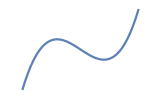
```mathematica
-Graphics-//FullForm
```

Graphics[List[List[List[],List[],Annotation[List[RGBColor[0.368417,0.506779,0.709798],AbsoluteThickness[1.6],Opacity[1.],Line[List[List[-2.64916,-79.9704],List[-2.63533,-77.8516],List[-2.51845,-61.7569],List[-2.39167,-46.2406],List[-2.27335,-33.4958],List[-2.14512,-21.4783],List[-2.01922,-11.3962],List[-2.01739,-11.2613],List[-2.01555,-11.1268],List[-2.01188,-10.8588],List[-2.00454,-10.3267],List[-1.98987,-9.27884],List[-1.96051,-7.24721],List[-1.90179,-3.43615],List[-1.8998,-3.31281],List[-1.89781,-3.18984],List[-1.89383,-2.94504],List[-1.88588,-2.45992],List[-1.86996,-1.50757],List[-1.83812,0.326257],List[-1.77446,3.71611],List[-1.7726,3.80954],List[-1.77074,3.90267],List[-1.76703,4.088],List[-1.7596,4.45502],List[-1.74474,5.17451],List[-1.71502,6.55586],List[-1.71316,6.63966],List[-1.7113,6.72317],List[-1.70759,6.88931],List[-1.70016,7.21805],List[-1.6853,7.86147],List[-1.65558,9.09266],List[-1.65376,9.1657],List[-1.65194,9.23848],List[-1.6483,9.3832],List[-1.64101,9.66936],List[-1.62645,10.2287],List[-1.59731,11.2956],List[-1.59549,11.36],List[-1.59367,11.4242],List[-1.59003,11.5517],List[-1.58274,11.8036],List[-1.56818,12.2948],List[-1.53904,13.2274],List[-1.53707,13.2883],List[-1.53509,13.3488],List[-1.53114,13.4691],List[-1.52324,13.706],List[-1.50743,14.1655],List[-1.47582,15.0282],List[-1.47384,15.0797],List[-1.47187,15.1308],List[-1.46792,15.2323],List[-1.46002,15.4318],List[-1.44421,15.8172],List[-1.4126,16.5341],List[-1.41076,16.5737],List[-1.40891,16.613],List[-1.40522,16.6911],List[-1.39785,16.8443],List[-1.3831,17.1393],List[-1.35361,17.6843],List[-1.35176,17.7164],List[-1.34992,17.7482],List[-1.34623,17.8113],List[-1.33886,17.9346],List[-1.32411,18.1704],List[-1.29462,18.599],List[-1.29262,18.626],List[-1.29062,18.6527],List[-1.28662,18.7054],List[-1.27863,18.8076],List[-1.26264,19.],List[-1.26065,19.0229],List[-1.25865,19.0455],List[-1.25465,19.0901],List[-1.24666,19.1761],List[-1.23067,19.3364],List[-1.22867,19.3553],List[-1.22667,19.374],List[-1.22268,19.4106],List[-1.21469,19.4809],List[-1.21269,19.4979],List[-1.21069,19.5146],List[-1.20669,19.5473],List[-1.1987,19.6099],List[-1.1967,19.625],List[-1.1947,19.6398],List[-1.19071,19.6687],List[-1.18271,19.7236],List[-1.16673,19.8222],List[-1.16477,19.8333],List[-1.1628,19.8441],List[-1.15888,19.8651],List[-1.15103,19.9045],List[-1.14907,19.9137],List[-1.14711,19.9228],List[-1.14319,19.9403],List[-1.13534,19.9726],List[-1.13338,19.9801],List[-1.13142,19.9874],List[-1.12749,20.0013],List[-1.12553,20.008],List[-1.12357,20.0144],List[-1.11965,20.0267],List[-1.11768,20.0325],List[-1.11572,20.038],List[-1.1118,20.0485],List[-1.10984,20.0535],List[-1.10788,20.0582],List[-1.10395,20.067],List[-1.10199,20.0711],List[-1.10003,20.0749],List[-1.09807,20.0786],List[-1.0961,20.082],List[-1.09414,20.0853],List[-1.09218,20.0883],List[-1.08826,20.0937],List[-1.0863,20.0961],List[-1.08433,20.0983],List[-1.08237,20.1003],List[-1.08041,20.1021],List[-1.07845,20.1036],List[-1.07649,20.105],List[-1.07453,20.1061],List[-1.07256,20.1071],List[-1.0706,20.1078],List[-1.06864,20.1083],List[-1.06668,20.1086],List[-1.06472,20.1088],List[-1.06276,20.1087],List[-1.06079,20.1084],List[-1.05883,20.1079],List[-1.05687,20.1072],List[-1.05491,20.1063],List[-1.05295,20.1052],List[-1.05099,20.1039],List[-1.04902,20.1023],List[-1.04706,20.1006],List[-1.0451,20.0987],List[-1.04314,20.0966],List[-1.04118,20.0943],List[-1.03935,20.0919],List[-1.03752,20.0894],List[-1.03386,20.0839],List[-1.03203,20.0808],List[-1.0302,20.0776],List[-1.02654,20.0707],List[-1.02471,20.067],List[-1.02288,20.0631],List[-1.01922,20.0548],List[-1.0119,20.0361],List[-1.01007,20.031],List[-1.00824,20.0258],List[-1.00459,20.0148],List[-0.997268,19.9907],List[-0.995438,19.9843],List[-0.993609,19.9777],List[-0.98995,19.964],List[-0.982632,19.9346],List[-0.980802,19.9269],List[-0.978973,19.9189],List[-0.975314,19.9026],List[-0.967995,19.868],List[-0.966166,19.8589],List[-0.964336,19.8497],List[-0.960677,19.8308],List[-0.953359,19.791],List[-0.95153,19.7806],List[-0.9497,19.7701],List[-0.946041,19.7487],List[-0.938723,19.7038],List[-0.924087,19.6065],List[-0.922103,19.5926],List[-0.920118,19.5784],List[-0.91615,19.5496],List[-0.908212,19.4899],List[-0.892338,19.3617],List[-0.890354,19.3449],List[-0.888369,19.328],List[-0.884401,19.2935],List[-0.876464,19.2224],List[-0.860589,19.072],List[-0.858605,19.0524],List[-0.85662,19.0327],List[-0.852652,18.9927],List[-0.844715,18.9107],List[-0.82884,18.7389],List[-0.797091,18.364],List[-0.795239,18.3408],List[-0.793387,18.3176],List[-0.789683,18.2706],List[-0.782274,18.1751],List[-0.767457,17.9777],List[-0.737824,17.5578],List[-0.735972,17.5305],List[-0.73412,17.5031],List[-0.730415,17.4478],List[-0.723007,17.3357],List[-0.70819,17.1055],List[-0.678556,16.6222],List[-0.676549,16.5883],List[-0.674543,16.5544],List[-0.670529,16.486],List[-0.662501,16.3477],List[-0.646446,16.0648],List[-0.614336,15.4741],List[-0.550115,14.1993],List[-0.424013,11.3784],List[-0.306371,8.44088],List[-0.178823,5.01901],List[-0.0597365,1.69076],List[0.0570117,-1.61379],List[0.183666,-5.15225],List[0.30186,-8.32349],List[0.42996,-11.5198],List[0.555721,-14.3153],List[0.557554,-14.353],List[0.559387,-14.3906],List[0.563052,-14.4656],List[0.570384,-14.6145],List[0.585046,-14.9076],List[0.614371,-15.4747],List[0.616204,-15.5093],List[0.618037,-15.5438],List[0.621703,-15.6124],List[0.629034,-15.7485],List[0.643696,-16.0155],List[0.673021,-16.5285],List[0.675009,-16.5623],List[0.676997,-16.5959],List[0.680972,-16.6627],List[0.688922,-16.7947],List[0.704823,-17.0522],List[0.736625,-17.5402],List[0.738612,-17.5694],List[0.7406,-17.5986],List[0.744575,-17.6564],List[0.752526,-17.7703],List[0.768426,-17.9909],List[0.800228,-18.4028],List[0.802084,-18.4256],List[0.803939,-18.4483],List[0.80765,-18.4932],List[0.815071,-18.5813],List[0.829915,-18.7508],List[0.83177,-18.7714],List[0.833625,-18.7918],List[0.837336,-18.8322],List[0.844758,-18.9112],List[0.859601,-19.0623],List[0.861456,-19.0805],List[0.863312,-19.0986],List[0.867023,-19.1343],List[0.874444,-19.2039],List[0.889287,-19.3358],List[0.891143,-19.3516],List[0.892998,-19.3673],List[0.896709,-19.3982],List[0.904131,-19.458],List[0.918974,-19.5702],List[0.920793,-19.5833],List[0.922612,-19.5962],List[0.926249,-19.6215],List[0.933525,-19.6704],List[0.935344,-19.6822],List[0.937162,-19.6939],List[0.9408,-19.7168],List[0.948076,-19.7607],List[0.949894,-19.7713],List[0.951713,-19.7817],List[0.955351,-19.8021],List[0.962626,-19.8409],List[0.977177,-19.911],List[0.978996,-19.919],List[0.980815,-19.9269],List[0.984453,-19.9422],List[0.991728,-19.9707],List[0.993547,-19.9775],List[0.995366,-19.984],List[0.999004,-19.9967],List[1.00628,-20.0199],List[1.0081,-20.0253],List[1.00992,-20.0306],List[1.01355,-20.0406],List[1.01537,-20.0453],List[1.01719,-20.0499],List[1.02083,-20.0585],List[1.02265,-20.0626],List[1.02447,-20.0665],List[1.02811,-20.0738],List[1.02992,-20.0771],List[1.03174,-20.0804],List[1.03538,-20.0863],List[1.03735,-20.0892],List[1.03933,-20.0919],List[1.0413,-20.0944],List[1.04328,-20.0968],List[1.04525,-20.0989],List[1.04722,-20.1008],List[1.0492,-20.1025],List[1.05117,-20.104],List[1.05314,-20.1053],List[1.05512,-20.1064],List[1.05709,-20.1073],List[1.05906,-20.1079],List[1.06104,-20.1084],List[1.06301,-20.1087],List[1.06499,-20.1088],List[1.06696,-20.1086],List[1.06893,-20.1083],List[1.07091,-20.1077],List[1.07288,-20.1069],List[1.07485,-20.1059],List[1.07683,-20.1048],List[1.0788,-20.1034],List[1.08077,-20.1017],List[1.08275,-20.0999],List[1.08472,-20.0979],List[1.0867,-20.0957],List[1.08867,-20.0932],List[1.09064,-20.0905],List[1.09262,-20.0877],List[1.09459,-20.0846],List[1.09854,-20.0777],List[1.10051,-20.074],List[1.10248,-20.0701],List[1.10643,-20.0615],List[1.10841,-20.0569],List[1.11038,-20.0521],List[1.11433,-20.0419],List[1.1163,-20.0364],List[1.11827,-20.0307],List[1.12222,-20.0187],List[1.13012,-19.9921],List[1.13209,-19.9849],List[1.13406,-19.9775],List[1.13801,-19.962],List[1.14591,-19.9283],List[1.14788,-19.9193],List[1.14985,-19.9101],List[1.1538,-19.891],List[1.16169,-19.8501],List[1.16354,-19.8401],List[1.16538,-19.8298],List[1.16906,-19.8087],List[1.17643,-19.7642],List[1.17827,-19.7525],List[1.18011,-19.7407],List[1.18379,-19.7164],List[1.19116,-19.6655],List[1.193,-19.6522],List[1.19484,-19.6388],List[1.19852,-19.6113],List[1.20589,-19.5538],List[1.22062,-19.4291],List[1.22246,-19.4126],List[1.2243,-19.3958],List[1.22799,-19.3618],List[1.23535,-19.2911],List[1.25008,-19.1397],List[1.27955,-18.7961],List[1.28154,-18.7708],List[1.28354,-18.7453],List[1.28753,-18.6935],List[1.29552,-18.5867],List[1.31149,-18.3608],List[1.31348,-18.3314],List[1.31548,-18.3018],List[1.31947,-18.2416],List[1.32746,-18.1182],List[1.34343,-17.8587],List[1.34542,-17.825],List[1.34742,-17.7911],List[1.35141,-17.7225],List[1.3594,-17.582],List[1.37537,-17.288],List[1.40731,-16.6472],List[1.40917,-16.6075],List[1.41103,-16.5677],List[1.41476,-16.4873],List[1.42222,-16.3235],List[1.43713,-15.984],List[1.46695,-15.2569],List[1.46882,-15.2093],List[1.47068,-15.1614],List[1.47441,-15.065],List[1.48187,-14.8689],List[1.49678,-14.4645],List[1.5266,-13.6056],List[1.52843,-13.5508],List[1.53026,-13.4957],List[1.53391,-13.3848],List[1.54122,-13.1599],List[1.55584,-12.6977],List[1.58508,-11.7232],List[1.58691,-11.66],List[1.58874,-11.5966],List[1.59239,-11.469],List[1.5997,-11.2106],List[1.61432,-10.6809],List[1.64356,-9.56968],List[1.64554,-9.49182],List[1.64753,-9.41363],List[1.65149,-9.25628],List[1.65942,-8.93769],List[1.67528,-8.28483],List[1.70699,-6.91572],List[1.77043,-3.91834],List[1.77228,-3.82563],List[1.77413,-3.73262],List[1.77783,-3.5457],List[1.78523,-3.16819],List[1.80003,-2.39848],List[1.82963,-0.799767],List[1.88883,2.63944],List[1.89084,2.76164],List[1.89284,2.88422],List[1.89685,3.13053],List[1.90487,3.62772],List[1.92091,4.64051],List[1.95299,6.74042],List[2.01714,11.2433],List[2.14312,21.3051],List[2.26063,32.2221],List[2.38804,45.8256],List[2.507,60.2735],List[2.62362,76.1587],List[2.64862,79.9639]]]],"Charting`Private`Tag$2997#1"]],List[],List[]],Rule[AspectRatio,Power[GoldenRatio,-1]],Rule[Axes,List[False,False]],Rule[AxesLabel,List[None,None]],Rule[AxesOrigin,List[0,0]],Rule[BaseStyle,List[]],Rule[DisplayFunction,Identity],Rule[Frame,List[List[None,None],List[None,None]]],Rule[FrameLabel,List[List[None,None],List[None,None]]],Rule[FrameTicks,List[List[Automatic,Charting`ScaledFrameTicks[List[Identity,Identity]]],List[Automatic,Charting`ScaledFrameTicks[List[Identity,Identity]]]]],Rule[GridLines,List[None,None]],Rule[GridLinesStyle,Directive[GrayLevel[0.5,0.4]]],Rule[ImagePadding,All],Rule[ImageSize,List[161.628,Automatic]],Rule[Method,List[Rule["DefaultBoundaryStyle",Automatic],Rule["DefaultMeshStyle",AbsolutePointSize[6]],Rule["ScalingFunctions",None],Rule["CoordinatesToolOptions",List[Rule["DisplayFunction",Function[List[Function[Identity[Slot[1]]][Part[Slot[1],1]],Function[Identity[Slot[1]]][Part[Slot[1],2]]]]],Rule["CopiedValueFunction",Function[List[Function[Identity[Slot[1]]][Part[Slot[1],1]],Function[Identity[Slot[1]]][Part[Slot[1],2]]]]]]]]],Rule[PlotRange,List[List[-3,3],List[-79.9704,79.9639]]],Rule[PlotRangeClipping,True],Rule[PlotRangePadding,List[List[Scaled[0.02],Scaled[0.02]],List[Scaled[0.05],Scaled[0.05]]]],Rule[Ticks,List[Automatic,Automatic]]]

```mathematica
ClearAll["Global`*"]
```

## 六步计算流程

当您按 Shift + Enter 时，总体计算器对表达式执行以下操作：

f[e1, e2, e3,...]

```mathematica
Grid[{
{Style["第一步：",Bold], "计算表达式的标头 (f)."},
{Style["第二步：",Bold],"按序计算所有元素 (e1, e2, e3 等) ——标准计算过程 \n
或 \n
按序计算选择的元素或不计算任何元素——非标准的计算过程"},
{Style["第三步：",Bold],"应用与 Orderless、Listable 和 Flat 相关联的变换."},
{Style["第四步：",Bold],"应用你给定的任何定义."},
{Style["第五步：",Bold],"应用内置定义."},
{Style["第六步：",Bold],"计算结果."}
},
Alignment->{{Center,Left}},BaseStyle->{FontFamily->"Times",FontColor->GrayLevel[0.15],FontSize->14},
Frame->True,
Background->RGBColor[1,1,0.85],
Spacings->{0.1,1},ItemSize->{{8,50},2}]
```

第一步： | 计算表达式的标头 (f).
第二步： | 按序计算所有元素 (e1, e2, e3 等) ——标准计算过程 

或 

按序计算选择的元素或不计算任何元素——非标准的计算过程
第三步： | 应用与 Orderless、Listable 和 Flat 相关联的变换.
第四步： | 应用你给定的任何定义.
第五步： | 应用内置定义.
第六步： | 计算结果.

请参阅教程 Evaluation.

## 计算标头（步骤1）

标头要先计算.

Example 1:

```mathematica
Print[x]
```

x

```mathematica
Echo[x]
```

x

x

```mathematica
(* 计算 f[x] *)
Echo[f][Echo[x]]
```

f

x

f[x]

Example 2:

```mathematica
(1*Plus+0)[10,20]
```

30

Example 3:

```mathematica
funs={Sin,Cos,Tan};
```

```mathematica
funs[[1]][10.0] (* funs[[1]] 首先计算 Sin *)
```

-0.544021

```mathematica
Sin[10.]
```

-0.544021

```mathematica
funs[[1]][10.0]//Trace
```

{{{funs,{Sin,Cos,Tan}},{Sin,Cos,Tan}⟦1⟧,Sin},Sin[10.],-0.544021}

## 计算元素（步骤 2）

### 标准计算

在标准计算中，将依次计算每个元素.

Example 1:

```mathematica
List[Echo[5],Echo[2],Echo[3]]
```

5

2

3

{5,2,3}

Example 2:

```mathematica
Clear[x,y,z];
x=1;
y=2;
z=3;
```

```mathematica
Plus[x,y,z]//Trace
```

{{x,1},{y,2},{z,3},1+2+3,6}

## 计算元素（步骤 2）

### 非标准计算

在非标准计算中，不计算元素或仅计算选定的元素.

对于某些函数，例如 Plot，不先计算参数是有意义的：

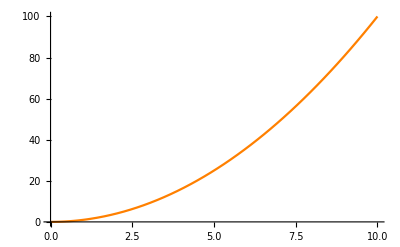

```mathematica
Clear[x];
x=2;
Plot[x^2,{x,0,10}]
```

如果先计算 x，绘图则变得无意义：

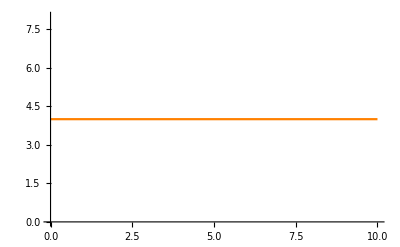

```mathematica
Plot[2^2,{x,0,10}]
```

同样，对于 Table，不应该先计算 x：

```mathematica
x=2;
Table[x^2,{x,0,10,1}]
```

{0,1,4,9,16,25,36,49,64,81,100}

对于If函数，则仅在开始时计算第一个参数：

```mathematica
Clear[x,y]
If[5>2,x=1,y=2];
```

```mathematica
{x,y}
```

{1,y}

```mathematica
Clear[x,y]
If[5<2,x=1,y=2];
```

```mathematica
{x,y}
```

{x,2}

## 应用属性（步骤 3）

在步骤 3 中，应用与属性 Orderless、Listable 和 Flat 相关的转换.

### Orderless

Orderless 属性打破了参数的规定顺序，并将其重新排列为规范顺序.

对应于运算的“可交换性”.

不相等：

```mathematica
ClearAll[f]
f[a,b]===f[b,a]
```

False

使用 Orderless 属性后相等：

```mathematica
SetAttributes[f,Orderless]
```

```mathematica
f[a,b]===f[b,a]
```

True

```mathematica
f[a,b,c,d]===f[a,c,b,d]===f[c,d,b,a]===f[d,a,b,c]
```

True

对参数进行排序：

```mathematica
{f[a,b],f[b,a]}
```

{f[a,b],f[a,b]}

```mathematica
{f[a,b,c,d],f[a,c,b,d],f[c,d,b,a],f[d,a,b,c]}
```

{f[a,b,c,d],f[a,b,c,d],f[a,b,c,d],f[a,b,c,d]}

范例——内置函数：

```mathematica
Attributes[Plus]
Attributes[Times]
```

{Flat,Listable,NumericFunction,OneIdentity,Orderless,Protected}

{Flat,Listable,NumericFunction,OneIdentity,Orderless,Protected}

```mathematica
a+b+c===c+a+b===b+a+c (* Plus *)
a*b*c===c*b*a===b*a*c (* Times *)
```

True

True

模式匹配中的顺序：

```mathematica
Cases[{a+10,b^2,20+a,c^2},a+_Integer]
```

{10+a,20+a}

```mathematica
{10*a,a*20}/.(a*x_Integer):>x^2*a
```

{100 a,400 a}

范例——自定义函数：

```mathematica
ClearAll[f1,x];
SetAttributes[f1,Orderless];
f1[x_Symbol,y_Integer,z_Real]:=y^z+x
```

```mathematica
{f1[x,3.0,2],f1[3.0,x,2],f1[2,3.0,x]}
```

{8.+x,8.+x,8.+x}

放大图像函数：

```mathematica
magnifyImage[img_Image,fact_Integer]:=Magnify[img,fact]
```

```mathematica
clock=ImageResize[ExampleData[{"TestImage","Clock"}],{100,100}]
```

-Graphics-

```mathematica
magnifyImage[clock,2] (* 如期所示 *)
```

-Graphics-

```mathematica
magnifyImage[2,clock] (* 不工作 *)
```

magnifyImage[2,-Graphics-]

使用 Orderless 属性：

```mathematica
SetAttributes[magnifyImage,Orderless];
magnifyImage[img_Image,fact_Integer]:=Magnify[img,fact]
```

```mathematica
magnifyImage[clock,2]
```

-Graphics-

```mathematica
magnifyImage[2,clock] (* this works as well *)
```

-Graphics-

## 应用属性（步骤 3）

### Listable

具有 Listable 属性的函数会自动遍历作为其参数出现的列表：

```mathematica
ClearAll[f1];
SetAttributes[f1,Listable]
```

```mathematica
f1[{a,b,c,d}]
```

{f1[a],f1[b],f1[c],f1[d]}

例如，Sin[]：

```mathematica
Sin[{10.0,20.0,30.0}]
Attributes[Sin]
```

{-0.544021,0.912945,-0.988032}

{Listable,NumericFunction,Protected}

在二维列表中：

```mathematica
f1[{{a,b,c,d},{e,f,g,h}}]
```

{{f1[a],f1[b],f1[c],f1[d]},{f1[e],f1[f],f1[g],f1[h]}}

有两个参数：

```mathematica
f1[{a,b,c,d},{e,f,g,h}]
```

{f1[a,e],f1[b,f],f1[c,g],f1[d,h]}

### Flat

如果同一函数的嵌套作为其参数，则具有 Flat 属性的函数将被展平：

```mathematica
ClearAll[f1]
SetAttributes[f1,Flat]
```

```mathematica
f1[a,f1[b,c],f1[f1[d,e],f],g]
```

f1[a,b,c,d,e,f,g]

Flat属性对于 Plus[] 和 Times[] 之类的函数是必需的，因为：

Plus[1,Plus[2,3,Plus[4,5]]] 等同于 Plus[1,2,3,4,5]
Times[1,Times[2,3,Times[4,5]]] 等同于 Times[1,2,3,4,5]

```mathematica
Column[Attributes[{Plus,Times}]]
```

```mathematica
{{{Flat,Listable,NumericFunction,OneIdentity,Orderless,Protected}}, {{Flat,Listable,NumericFunction,OneIdentity,Orderless,Protected}}}
```

注意， Flatten[] 可以完成相同的运算：

```mathematica
f2[a,f2[b,c],f2[f2[d,e],f],g]//Flatten
```

f2[a,b,c,d,e,f,g]

#### 在定义之前应用 Flat

```mathematica
ClearAll[f]
f[x_,y_,z_]:=f[x,y];
f[a_,b_,c_,d_]:={a,b,c,d};
Attributes[f]={Flat};
```

```mathematica
f[f[a,b],f[c,f[d,e]]]//Trace
```

{{f[c,f[d,e]],f[c,d,e],f[c,d]},f[f[a,b],f[c,d]],f[a,b,c,d],{a,b,c,d}}

## 应用定义（步骤 4 和 5）

在步骤 4 和 5 中，分别应用了自定义和内置定义.

自定义：

```mathematica
ClearAll[f];
f[a_,b_,c_]:=a*b*c
```

```mathematica
x=1;
y=2;
z=3;
f[x,y,z]
```

6

```mathematica
f[x,y,z]//Trace
```

{{x,1},{y,2},{z,3},f[1,2,3],2 3,6}

内置定义：

```mathematica
x=1;
y=2;
z=3;
Plus[x,y,z]
```

6

```mathematica
Plus[x,y,z]//Trace
```

{{x,1},{y,2},{z,3},1+2+3,6}

自定义先于内置定义：

```mathematica
Unprotect[Sin];
Sin[Pi/2]:=n1 (* 自定义 *)
Protect[Sin];
```

```mathematica
Quit[]
```

```mathematica
Sin[Pi/2]
```

1

```mathematica
Sin[Pi]
```

0

```mathematica
??Sin
```

Plus 附加了新的定义；f1 和 f2 设置为 Listable 函数：

```mathematica
SetAttributes[{f1,f2},Listable]
Unprotect[Plus];
f1[x_]+f2[y_]:=g[x y] (* custom definition *)
Protect[Plus];
```

```mathematica
f1[{1,2,3}]+f2[{4,5,6}]
```

{g[4],g[10],g[18]}

```mathematica
??Plus
```

## 计算结果（步骤 6）

应用定义后，将执行结果中的任何剩余计算：

```mathematica
ClearAll[f]
Attributes[f]={HoldAll};
f[x_]:=Sin[x]
```

```mathematica
k=10.0;
f[k]
```

-0.544021

```mathematica
f[k]//Trace
```

{f[k],Sin[k],{k,10.},Sin[10.],-0.544021}

## 显示所有步骤的示例

尝试确定以下示例中的步骤：

```mathematica
x=15;
y=10;
z=5;
```

```mathematica
fn=Plus;
```

```mathematica
fn[x,y,z]
```

30

-----------------------------------------------------------------------------------------------------------------

-------------------------------------------------- -------------------------------------------------- -------------

（第一步）将 fn 当作 Plus ：

```mathematica
fn[x,y,z]//Trace
```

```mathematica
{{fn,Plus},{x,15},{y,10},{z,5},15+10+5,30}
```

-----------------------------------------------------------------------------------------------------------------

-------------------------------------------------- -------------------------------------------------- -------------

（第二步）计算 x、y 和 z：

```mathematica
fn[x,y,z]//Trace
```

```mathematica
{{fn,Plus},{x,15},{y,10},{z,5},15+10+5,30}
```

-----------------------------------------------------------------------------------------------------------------

-------------------------------------------------- -------------------------------------------------- -------------

（第三步）应用 Orderless 属性：

{15，10，5} 变为 {5，10，15}.

（使用 Trace 无法看到.）

-----------------------------------------------------------------------------------------------------------------

-------------------------------------------------- -------------------------------------------------- -------------

应用 Plus 的定义并计算结果（第五步和第六步；第四步没有作任何事）：

```mathematica
fn[x,y,z]//Trace
```

```mathematica
{{fn,Plus},{x,15},{y,10},{z,5},15+10+5,30}
```

-----------------------------------------------------------------------------------------------------------------

-------------------------------------------------- -------------------------------------------------- -------------

# 非标准计算

## 选择性计算

当至少一个元素未被计算时，该计算称为非标准计算：

f[e1, e2, e3,...]

```mathematica
Grid[{
{Style["第一步：",Bold], "计算表达式的标头 (f)."},
{Style["第二步：",Bold],Column[{"按序计算所有元素 (e1, e2, e3 等) ——标准计算过程 \n
或 \n",
Style["按序计算选择的元素或不计算任何元素——非标准的计算过程",Bold]},BaselinePosition->Scaled[0.855]]},
{Style["第三步：",Bold],"应用与 Orderless、Listable 和 Flat 相关联的变换."},
{Style["第四步：",Bold],"应用你给定的任何定义."},
{Style["第五步：",Bold],"应用内置定义."},
{Style["第六步：",Bold],"计算结果."}
},
Alignment->{{Center,Left}},BaseStyle->{FontFamily->"Times",FontColor->GrayLevel[0.15],FontSize->14},
Frame->True,
Background->RGBColor[1,1,0.85],
Spacings->{0.1,1},ItemSize->{{8,55},2}]
```

第一步： | 计算表达式的标头 (f).
第二步： | 按序计算所有元素 (e1, e2, e3 等) ——标准计算过程 

或 

按序计算选择的元素或不计算任何元素——非标准的计算过程
第三步： | 应用与 Orderless、Listable 和 Flat 相关联的变换.
第四步： | 应用你给定的任何定义.
第五步： | 应用内置定义.
第六步： | 计算结果.

Plot：所有元素均未被计算：

```mathematica
Clear[x];
x=2;
Plot[x^2,{x,0,10}]
```

-Graphics-

Table：所有元素均未被计算：

```mathematica
x=2;
Table[x^2,{x,0,10,1}]
```

{0,1,4,9,16,25,36,49,64,81,100}

If：第二和第三元素均未被计算：

```mathematica
Clear[x,y]
If[5>2,x=1,y=2];
```

```mathematica
{x,y}
```

{1,y}

```mathematica
Clear[x,y]
If[5<2,x=1,y=2];
```

```mathematica
{x,y}
```

{x,2}

SetDelayed: 不计算第二个元素：

```mathematica
SetDelayed[x,RandomInteger[10]] (* x:=RandomInteger[10] *)
```

```mathematica
{x,x,x}
```

## 控制计算的属性

控制元素计算/保持的三个主要属性是：HoldFirst、HoldRest 和 HoldAll.

HoldFirst：保持第一个元素：

```mathematica
Clear[x,y,z];
x=1;
y=2;
z=3;
```

```mathematica
ClearAll[f1]
SetAttributes[f1,HoldFirst]
f1[x,y,z]
```

f1[x,2,3]

```mathematica
f11[x,y,z]
```

f11[1,2,3]

HoldRest：保持除第一个元素外的所有元素：

```mathematica
ClearAll[f2]
SetAttributes[f2,HoldRest]
f2[x,y,z]
```

f2[1,y,z]

HoldAll：保持所有元素：

```mathematica
ClearAll[f3]
SetAttributes[f3,HoldAll]
f3[x,y,z]
```

f3[x,y,z]

相关属性：NHoldFirst、NHoldRest、NHoldAll、SequenceHold、HoldAllComplete：

```mathematica
ClearAll[f4]
SetAttributes[f4,SequenceHold]
```

```mathematica
x=3;y=4;
f4[Sequence[1,2],x,y]
```

f4[Sequence[1,2],3,4]

```mathematica
SetAttributes[f5,HoldAll]
```

```mathematica
f5[Sequence[1,2],x,y]
```

f5[1,2,x,y]

## 仔细研究内置函数

各种内置函数严重依赖 Hold * 属性来执行各自的任务.

#### Table 的作用域

Table 从 HoldAll 属性获取其作用域能力：

```mathematica
Attributes[Table]
```

{HoldAll,Protected}

```mathematica
i=2;
Table[i^2,{i,1,5}]
```

{1,4,9,16,25}

如果允许对第一个参数求值：

```mathematica
ClearAttributes[Table,HoldAll];
SetAttributes[Table,HoldRest];
```

```mathematica
Table[i^2,{i,1,5}]
```

{1,4,9,16,25}

如果允许计算迭代器：

```mathematica
ClearAttributes[Table,HoldRest]
```

```mathematica
Table[i^2,{i,1,5}]
```

{1,4,9,16,25}

```mathematica
SetAttributes[Table,HoldAll]
```

#### Plot 的作用域

Plot 使用 HoldAll 属性对变量进行本地化：

```mathematica
Attributes[Plot]
```

{HoldAll,Protected,ReadProtected}

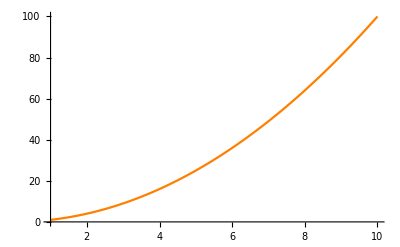

```mathematica
i=2;
Plot[i^2,{i,1,10}]
```

删除 HoldAll 属性时，将对参数进行计算：

```mathematica
ClearAttributes[Plot,HoldAll];
SetAttributes[Plot,HoldRest];
```

```mathematica
i=2;
Plot[i^2,{i,1,10}]
```

-Graphics-

```mathematica
ClearAttributes[Plot,HoldRest];
SetAttributes[Plot,HoldAll];
```

#### If 的功能

If 使用 HoldRest 属性保存第二个和第三个参数：

```mathematica
Attributes[If]
```

{HoldRest,Protected}

```mathematica
Clear[x,y]
If[5>2,x=1,y=2];
```

```mathematica
{x,y}
```

如果If 没有 HoldRest 属性：

```mathematica
ClearAttributes[If,HoldRest];
```

```mathematica
Clear[x,y]
If[5>2,x=1,y=2];
```

```mathematica
{x,y}
```

{1,y}

```mathematica
SetAttributes[If,HoldRest];
```

#### SetDelayed 的延迟计算

SetDelayed 使用 HoldAll 属性执行延迟计算：

```mathematica
Attributes[SetDelayed]
```

{HoldAll,Protected,SequenceHold}

```mathematica
ClearAll[x];
x:=RandomInteger[10]
```

```mathematica
{x,x,x}
```

{4,3,7}

如果用 HoldFirst 属性替换 HoldAll，则 SetDelayed 变为 Set：

```mathematica
ClearAttributes[SetDelayed,HoldAll];
SetAttributes[SetDelayed,HoldFirst];
```

```mathematica
ClearAll[x];
x:=RandomInteger[10]
```

```mathematica
{x,x,x,x,x}
```

{10,0,0,9,5}

```mathematica
ClearAttributes[SetDelayed,HoldFirst];
SetAttributes[SetDelayed,HoldAll];
```

## 具有 Hold * 属性的自定义函数

回想一下，在非标准计算中，可以使用 HoldFirst、HoldRest 或 HoldAll 属性保留一个或多个参数.

在需要时保持参数：

符号式传递

更新变量

#### 示例 1：跟踪动态变量

```mathematica
ClearAll[recordPoints,var];
 SetAttributes[recordPoints,HoldRest] 

recordPoints[head_Symbol,pointsVar_Symbol]:=DynamicModule[{x={0,0}},Column[{head[Dynamic[x,(x=#;AppendTo[pointsVar,#])&]]}],Initialization:>(pointsVar={})]
```

```mathematica
recordPoints[Slider,var]
```

```mathematica
var
```

{0.,0.004,0.03,0.056,0.133,0.239,0.297,0.366,0.546,0.604,0.662,0.741,0.779,0.818,0.881,0.914,0.946,0.972,0.981,0.989,0.995,0.999,1.,0.992,0.973,0.897,0.734,0.431,0.275,0.187,0.098,0.005,0.}

```mathematica
recordPoints[Slider2D,var]
```

```mathematica
var
```

{{0.045,0.03},{0.05,0.03},{0.055,0.03},{0.065,0.025},{0.075,0.02},{0.08,0.015},{0.09,0.015},{0.1,0.015},{0.105,0.01},{0.115,0.005},{0.13,0.005},{0.14,0.},{0.145,0.},{0.155,0.},{0.165,0.},{0.17,0.},{0.18,0.},{0.195,0.},{0.205,0.},{0.215,0.},{0.235,0.},{0.24,0.},{0.25,0.},{0.28,0.},{0.285,0.},{0.295,0.},{0.305,0.},{0.31,0.},{0.32,0.},{0.335,0.},{0.34,0.},{0.355,0.},{0.375,0.},{0.395,0.},{0.405,0.},{0.415,0.},{0.44,0.},{0.48,0.},{0.49,0.},{0.505,0.},{0.53,0.005},{0.545,0.015},{0.56,0.02},{0.585,0.03},{0.61,0.045},{0.665,0.075},{0.675,0.08},{0.685,0.085},{0.7,0.095},{0.74,0.115},{0.765,0.13},{0.775,0.14},{0.79,0.15},{0.815,0.16},{0.84,0.18},{0.855,0.19},{0.865,0.2},{0.87,0.2},{0.87,0.205},{0.87,0.21},{0.87,0.215},{0.87,0.22},{0.875,0.24},{0.88,0.25},{0.885,0.26},{0.89,0.28},{0.895,0.295},{0.895,0.3},{0.895,0.31},{0.895,0.34},{0.9,0.365},{0.9,0.38},{0.91,0.435},{0.915,0.46},{0.92,0.485},{0.925,0.52},{0.93,0.555},{0.93,0.56},{0.93,0.565},{0.93,0.57},{0.93,0.575},{0.93,0.59},{0.93,0.615},{0.915,0.67},{0.91,0.69},{0.905,0.7},{0.9,0.72},{0.9,0.735},{0.895,0.745},{0.89,0.745},{0.885,0.745},{0.885,0.75},{0.885,0.755},{0.88,0.755},{0.865,0.775},{0.815,0.84},{0.775,0.885},{0.76,0.895},{0.745,0.915},{0.715,0.945},{0.71,0.955},{0.7,0.96},{0.68,0.98},{0.665,0.995},{0.66,1.},{0.655,1.},{0.645,1.},{0.615,1.},{0.61,1.},{0.58,1.},{0.56,1.},{0.55,1.},{0.54,1.},{0.52,1.},{0.505,1.},{0.47,1.},{0.46,1.},{0.44,1.},{0.43,1.},{0.415,1.},{0.41,1.},{0.395,1.},{0.375,1.},{0.37,1.},{0.36,1.},{0.34,1.},{0.325,1.},{0.305,1.},{0.3,1.},{0.29,1.},{0.27,1.},{0.24,1.},{0.23,1.},{0.215,0.995},{0.2,0.99},{0.185,0.975},{0.175,0.965},{0.165,0.96},{0.16,0.955},{0.15,0.945},{0.15,0.94},{0.145,0.935},{0.145,0.93},{0.14,0.93},{0.14,0.925},{0.135,0.915},{0.13,0.91},{0.125,0.9},{0.12,0.88},{0.115,0.87},{0.11,0.855},{0.105,0.835},{0.095,0.815},{0.09,0.795},{0.075,0.75},{0.07,0.72},{0.07,0.71},{0.07,0.695},{0.065,0.67},{0.065,0.665},{0.065,0.65},{0.065,0.63},{0.065,0.595},{0.065,0.585},{0.065,0.565},{0.065,0.55},{0.065,0.545},{0.065,0.525},{0.065,0.505},{0.065,0.5},{0.07,0.485},{0.07,0.48},{0.085,0.445},{0.09,0.425},{0.095,0.415},{0.105,0.38},{0.115,0.365},{0.13,0.335},{0.135,0.31},{0.155,0.275},{0.16,0.26},{0.17,0.255},{0.18,0.235},{0.2,0.215},{0.21,0.2},{0.23,0.185},{0.235,0.18},{0.245,0.175},{0.25,0.17},{0.265,0.155},{0.275,0.15},{0.28,0.145},{0.285,0.145},{0.295,0.14},{0.3,0.135},{0.31,0.135},{0.32,0.13},{0.35,0.12},{0.355,0.115},{0.37,0.115},{0.385,0.11},{0.385,0.105},{0.395,0.1},{0.4,0.1},{0.405,0.1},{0.41,0.1}}

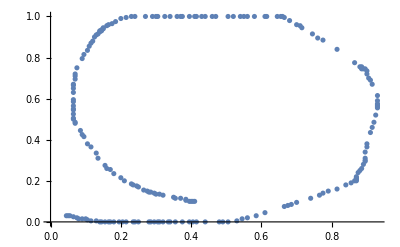

```mathematica
ListPlot[var]
```

```mathematica
recordPoints[VerticalSlider,var]
```

```mathematica
var
```

{0.,0.004,0.026,0.082,0.164,0.19,0.254,0.274,0.292,0.324,0.404,0.426,0.452,0.524,0.55,0.572,0.616,0.64,0.666,0.718,0.74,0.766,0.808,0.834,0.864,0.872,0.906,0.914,0.92,0.926,0.928,0.93,0.928,0.926,0.924,0.922,0.916,0.898,0.884,0.868,0.764,0.722,0.7,0.61,0.566,0.518,0.442,0.408,0.376,0.316,0.286,0.26,0.21,0.194,0.182,0.158,0.148,0.138,0.116,0.104,0.092,0.074,0.066,0.058,0.044,0.042,0.038,0.036,0.032,0.026,0.022,0.018,0.012,0.01,0.006,0.004}

#### 示例 2：纯函数的属性

以下方法不能创建随机整数列表：

```mathematica
ClearAll[f1]
f1=Table[#,10]&;
f1[RandomInteger[10]]
```

{10,10,10,10,10,10,10,10,10,10}

默认情况下，纯函数在计算求值时计算参数.

使用 HoldFirst 属性：

```mathematica
ClearAll[f1]
f1=Function[x,Table[x,10],HoldFirst];
f1[RandomInteger[10]]
```

{0,8,0,6,2,3,8,5,4,6}

#### 示例 3：自定义绘图功能

```mathematica
x=10;

plotC[fun_,range_]:=Graphics[Line[Table[{range[[1]],fun},range]],Axes->True,AspectRatio->0.8]
```

```mathematica
plotC[x^3,{x,0,10}] (* 结果出错：x 被计算，plotC 变得无效 *)
```

Table::itraw: 原始对象 10 不能作为迭代器使用.

-Graphics-

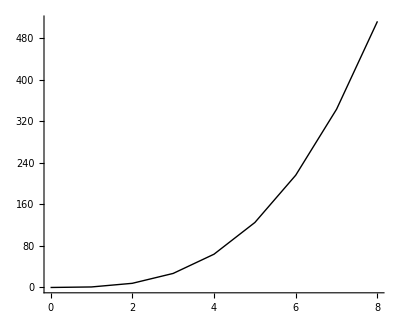

```mathematica
SetAttributes[plotC,HoldAll]
plotC[x^3,{x,0,8}]
```

#### 示例 4：updateList 函数

```mathematica
list={1,2,3}
```

{1,2,3}

```mathematica
ClearAll[updateList];
SetAttributes[updateList,HoldFirst]; 
updateList[l_,fact_]:=(l={l[[1]]+fact*l[[2]],l[[2]]+fact*l[[3]],l[[3]]+fact*l[[1]]})
```

```mathematica
updateList[list,5] (* 1 + 5*2, 2 +5*3, 3 + 5*1 *)
```

{11,17,8}

```mathematica
list
```

{11,17,8}

```mathematica
updateList[list,5]
```

{96,57,63}

```mathematica
list
```

{96,57,63}

## 覆盖 Hold* 属性

有时您需要在具有 Hold * 属性的函数中强制计算参数：

```mathematica
Quit[]
```

```mathematica
ClearAll[f,x];
SetAttributes[f,HoldAll]
```

```mathematica
x=10;
f[x]
```

f[x]

方法 1：您可以使用 Evaluate[] 强制执行计算：

```mathematica
f[Evaluate[x]]
```

f[10]

方法 2：使用 ReplaceAll：

```mathematica
f[y]/.y->10
```

f[10]

方法 3：使用 With[]：

```mathematica
With[{y=10},f[y]]
```

f[10]

方法 4：使用“注入器模式”：

```mathematica
10/.num_:>f[num]
```

f[10]

#### 示例 1：Plot 内的符号计算

替换迭代器值后，各种绘图函数会计算函数，因此以下操作无效：

```mathematica
Plot[D[Sin[x],x],{x,0,10}]
```

General::ivar: 0.000204286 不是一个有效的变量.

General::ivar: 0.204286 不是一个有效的变量.

General::ivar: 0.408368 不是一个有效的变量.

General::stop: 在本次计算中，General::ivar 的进一步输出将被抑制.

-Graphics-

```mathematica
RegionPlot[Integrate[y/(2 Sqrt[x y]),x]<1,{x,-2,2},{y,-2,2}]
```

Integrate::ilim: 10 中有无效的积分变量或者极限值.

Integrate::ilim: -1.99979 中有无效的积分变量或者极限值.

General::stop: 在本次计算中，Integrate::ilim 的进一步输出将被抑制.

-Graphics-

与 Evaluate 一起使用：

```mathematica
Clear[x]
```

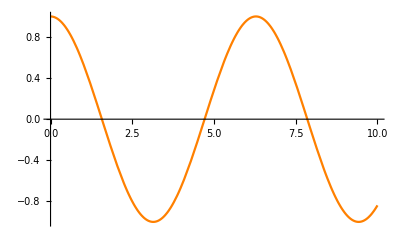

```mathematica
Plot[Evaluate[D[Sin[x],x]],{x,0,10}]
```

```mathematica
Clear[y]
```

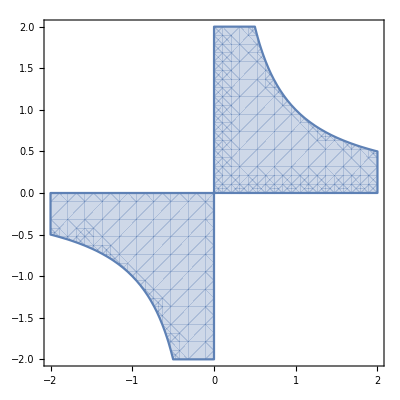

```mathematica
RegionPlot[Evaluate[Integrate[y/(2 Sqrt[x y]),x]<1],{x,-2,2},{y,-2,2}]
```

#### 示例 2：在 Plot 中设置表达式列表的样式

除非提供明确的列表结构，否则 Plot 函数会使用统一样式.

List 结构对 Plot 和 RegionPlot 不可见：

```mathematica
Table[x^i,{i,1,4}]
```

{x,x^2,x^3,x^4}

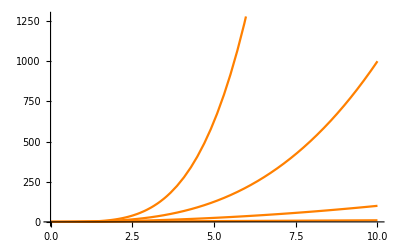

```mathematica
Plot[Table[x^i,{i,1,4}],{x,0,10},PlotLegends->"Expressions"]
```

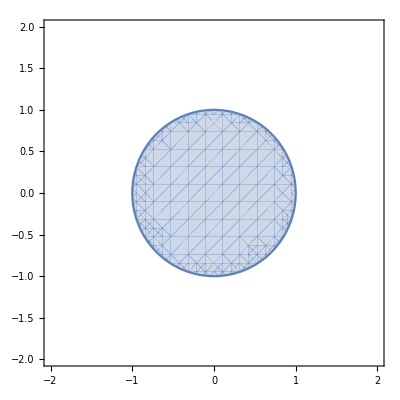

```mathematica
RegionPlot[Table[x^2+y^2<n,{n,1,3}],{x,-2,2},{y,-2,2},PlotLegends->"Expressions"]
```

Evaluate [] 使列表结构表现出来：

```mathematica
Quit
```

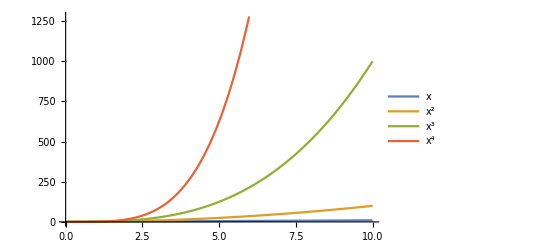

```mathematica
Plot[Evaluate[Table[x^i,{i,1,4}]],{x,0,10},PlotLegends->"Expressions"]
```

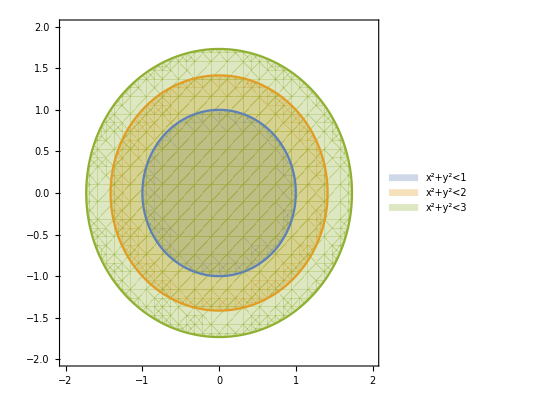

```mathematica
RegionPlot[Evaluate[Table[x^2+y^2<n,{n,1,3}]],{x,-2,2},{y,-2,2},PlotLegends->"Expressions"]
```

#### 示例 3：注入预先构造的选项

以下插入选项的方法不适用于具有 HoldAll 属性的函数：

```mathematica
plotOptions={PlotPoints->10,MaxRecursion->2,PlotStyle->Red};
Plot[x^2,{x,0,10},plotOptions]
```

Plot::nonopt: Plot[x^2,{x,0,10},plotOptions] 中位置 2 外应该是选项（而不是 plotOptions）. 选项必须是一个规则或者规则列表.

Plot[x^2,{x,0,10},plotOptions]

```mathematica
nintegrateOptions={ Exclusions->(Sin[x^2+y]==0),WorkingPrecision->10};
NIntegrate[1/(√Sin[x^2+y]),{x,-5,5},{y,-5,5}, nintegrateOptions]
```

NIntegrate::ilim: {Exclusions→Sin[x^2+y]==0,WorkingPrecision→10} 中有无效的积分变量或者极限值.

NIntegrate[1/(√Sin[x^2+y]),{x,-5,5},{y,-5,5},nintegrateOptions]

```mathematica
Attributes[{Plot,NIntegrate}]//Column
```

{HoldAll,Protected,ReadProtected}
{HoldAll,Protected}

您需要首先计算列表：

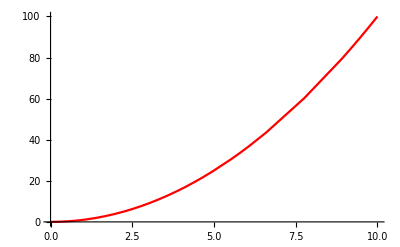

```mathematica
Plot[x^2,{x,0,10},Evaluate[plotOptions]]
```

```mathematica
NIntegrate[1/(√Sin[x^2+y]),{x,-5,5},{y,-5,5}, Evaluate[nintegrateOptions]]
```

81.84747968-84.70573498 ⅈ

#### 示例 4：来自变量的纯函数

以下定义函数的方法不起作用：

```mathematica
expr=x^2+2 x+1
```

1+2 x+x^2

```mathematica
fun1=Function[{x},expr]
```

Function[{x},expr]

```mathematica
fun1[5]
```

1+2 x+x^2

Function[] 不计算参数：

```mathematica
Attributes[Function]
```

{HoldAll,Protected}

可以通过计算参数来修正：

```mathematica
fun2=Function[{x},Evaluate[expr]]
```

Function[{x},1+2 x+x^2]

```mathematica
fun2[5]
```

#### 示例 5：具有 HoldAll 属性的函数列表

迭代器无法在 f 内注入值，因为它具有 HoldAll 属性：

```mathematica
ClearAll[f];
SetAttributes[f,HoldAll];
```

```mathematica
Table[f[i],{i,1,5}]
```

{f[i],f[i],f[i],f[i],f[i]}

纯函数列表：

```mathematica
Attributes[Function]
```

{HoldAll,Protected}

以下方法行不通——i 仍然没有被计算：

```mathematica
a={10,20,30,40,50};
```

```mathematica
fnList1=Table[a[[i]]*Sin[#]&,{i,5}]
```

{a⟦i⟧ Sin[#1]&,a⟦i⟧ Sin[#1]&,a⟦i⟧ Sin[#1]&,a⟦i⟧ Sin[#1]&,a⟦i⟧ Sin[#1]&}

```mathematica
fnList1[[1]][10.0]
```

Part::pkspec1: 表达式 i 不能作为部分指定使用.

-0.544021 {10,20,30,40,50}⟦i⟧

使用“注入器模式”：

```mathematica
fnList2=Range[5]/.(x_Integer:>(a[[x]]*Sin[#]&))
```

{a⟦1⟧ Sin[#1]&,a⟦2⟧ Sin[#1]&,a⟦3⟧ Sin[#1]&,a⟦4⟧ Sin[#1]&,a⟦5⟧ Sin[#1]&}

```mathematica
fnList2[[1]][10.0]
```

-5.44021

滑块列表：

```mathematica
Attributes[Dynamic]
```

文档中的示例：动态简介.

以下用于创建滑块列表的方法不起作用：

```mathematica
data={.1,.5,.3,.9,.2};
```

```mathematica
Table[Slider[Dynamic[data[[i]]]],{i,5}]
```

{,,,,}

```mathematica
Attributes[Dynamic]
```

{HoldFirst,Protected,ReadProtected}

您可以计算参数，例如，使用 With []：

```mathematica
Table[With[{i1=i},Slider[Dynamic[data[[i1]]]]],{i,5}]
```

{,,,,}

# 使用未被计算的表达式

## 防止计算的函数

Wolfram 语言使您可以使用表达式未被计算的形式.

Hold

HoldForm

Inactivate

Unevaluated

Defer

HoldPattern

### Hold

Hold 保留一个未被计算的表达式：

```mathematica
Hold[1+2+3]
```

Hold[1+2+3]

```mathematica
Hold[Expand[(a+b)^10]]
```

Hold[Expand[(a+b)^10]]

从表达式中提取原子：

```mathematica
Cases[Hold[2.5^2+3.5^3+4.5^4+5.5^5], _Integer,Infinity]
```

{2,3,4,5}

```mathematica
Cases[Hold[2.5^2+3.5^3+4.5^4+5.5^5], _Real,Infinity]
```

{2.5,3.5,4.5,5.5}

ReleaseHold 释放保持：

```mathematica
Hold[1+2+3]
ReleaseHold[%]
```

Hold[1+2+3]

6

### HoldForm

HoldForm 保留一个未被计算的表达式，并且显示时不使用封装：

```mathematica
HoldForm[1+2+3]
```

1+2+3

```mathematica
HoldForm[x=10] (* 显示赋值 *)
```

x=10

```mathematica
HoldForm[x^2+x+1=10] (* 显示方程 *)
```

x^2+x+1=10

```mathematica
FullForm[10^4+4 10^3 20+6 10^2 20^2]
```

330000

```mathematica
HoldForm[FullForm[10^4+4 10^3 20+6 10^2 20^2]] (* 显示完整格式 *)
```

Plus[Power[10,4],Times[4,Power[10,3],20],Times[6,Power[10,2],Power[20,2]]]

```mathematica
∑_(i=1)^10 (HoldForm[#1^2]&)[i]
```

1^2+2^2+3^2+4^2+5^2+6^2+7^2+8^2+9^2+10^2

## 防止计算的函数（续）

### Inactivate

Inactivate 通过使一个或多个标头失效来防止计算：

```mathematica
Inactivate[1+2+3] (* Plus 失效*)
```

1+2+3

```mathematica
Inactivate[1+2*3] (* Plus 和 Times 失效*)
```

1+2×3

```mathematica
Inactivate[1+2*3,Plus] (* 只有 Plus 失效*)
```

1+6

```mathematica
Inactivate[Sum[1/n^4,{n,1,Infinity}],Sum]==Sum[1/n^4,{n,1,Infinity}]// TraditionalForm(* 等同性 *)
```

1/n^4n1∞==π^4/90

```mathematica
Inactivate[D[f[g[x]],x],D]==D[f[g[x]],x] // TraditionalForm (* 链式法则 *)
```

(∂f(g(x)))/(∂x)==g'(x) f'(g(x))

```mathematica
Inactivate[1+2+3] 
Activate[%]
```

1+2+3

6

## 防止计算的函数（续）

### Unevaluated

Unevaluated 保持未计算的表达式，当用在函数的参数中时表示未计算的格式：

```mathematica
Unevaluated[1+2+3]
```

Unevaluated[1+2+3]

```mathematica
Head[Unevaluated[1+2+3]]
```

Plus

与 Hold/HoldForm 的对比：

```mathematica
{Head[Hold[1+1]],Head[HoldForm[1+1]]}
```

{Hold,HoldForm}

#### 示例 1：表达式/变量名的长度

```mathematica
1+2+3+4+5
```

15

```mathematica
Length[1+2+3+4+5]
```

0

```mathematica
Length[Unevaluated[1+2+3+4+5]]
```

5

由于使用了 Unevaluated []，Length 将 1 + 2 + 3 + 4 +5作为参数，并且它不计算表达式：

```mathematica
variableWithLongName=100;
StringLength[ToString[Unevaluated[variableWithLongName]]]
```

20

#### 示例 2：将未计算的映射到列表

表达式列表的长度：

```mathematica
Length/@Unevaluated[{10+20,10+20+30,10+20+30+40,10+20+30+40+50}]
```

{0,0,0,0}

```mathematica
Length/@Unevaluated/@Unevaluated[{10+20,10+20+30,10+20+30+40,10+20+30+40+50}]
```

{2,3,4,5}

为了防止由于 Map 而导致的计算，需要额外的 Unevaluated：

```mathematica
Map[Unevaluated,{10+20,10+20+30,10+20+30+40,10+20+30+40+50}]
```

{Unevaluated[30],Unevaluated[60],Unevaluated[100],Unevaluated[150]}

```mathematica
Map[Unevaluated,Unevaluated[{10+20,10+20+30,10+20+30+40,10+20+30+40+50}]]
```

{Unevaluated[10+20],Unevaluated[10+20+30],Unevaluated[10+20+30+40],Unevaluated[10+20+30+40+50]}

变量列表的长度：

```mathematica
{var112,var298347234,var2324,var93485793,var848488}={1,2,3,4,5};
```

```mathematica
StringLength/@ToString/@Unevaluated/@Unevaluated[{var112,var298347234,var2324,var93485793,var848488}]
```

{6,12,7,11,9}

#### 示例 3：使用 Thread

按预期工作:

```mathematica
Thread[Equal[{a,b,c},{1,2,3}]]
```

{a==1,b==2,c==3}

如果使用 Print[] 也可以获得类似的输出会很好. Thread 首先计算参数：

```mathematica
Thread[Print[{a,b,c}," = ",{1,2,3}]]
```

{a,b,c} = {1,2,3}

可以使用 Unevaluated 的方法解决：

```mathematica
Thread[Unevaluated[Print[{a,b,c}," = ",{1,2,3}]]]
```

a = 1

b = 2

c = 3

{Null,Null,Null}

Equal 和 Max 也一样：

```mathematica
Thread[{1,2,3}=={3,2,1}]
```

False

```mathematica
Thread[Unevaluated[{1,2,3}=={3,2,1}]]
```

{False,True,False}

```mathematica
Thread[Max[{2,3,5,4,1,8,7},{1,4,6,3,2,8,8}]]
```

8

```mathematica
Thread[Unevaluated[Max[{2,3,5,4,1,8,7},{1,4,6,3,2,8,8}]]]
```

{2,4,6,4,2,8,8}

## 防止计算的函数（续）

### Defer

Defer 显示一个未被计算的格式（将来会被计算）：

```mathematica
Defer[1+2+3]
```

1+2+3

```mathematica
1+2+3
```

6

```mathematica
CreateDocument[Defer[1+1]]
```

hjakf_shm89FrontEndObject[LinkObject["hjakf_shm", 3, 1]]89未命名-10

### HoldPattern

HoldPattern 阻止模式计算.

模式对象的计算与其他对象一样：

```mathematica
_+_+_
```

3 _

```mathematica
Log[_]/Log[_]
```

1

使用 HoldPattern 可以防止计算：

```mathematica
HoldPattern[_+_]
HoldPattern[Log[_]/Log[_]]
```

HoldPattern[_+_]

HoldPattern[Log[_]/Log[_]]

替换内部保留表达式：

```mathematica
Hold[{1,2+3,4,5+6,7}]/.HoldPattern[_+_]:>x
```

Hold[{1,x,4,x,7}]

从 Cases 中选择规则：

```mathematica
NSolve[x^5-2x+1==0,x]//Flatten
```

{x→-1.29065,x→-0.114071-1.21675 ⅈ,x→-0.114071+1.21675 ⅈ,x→0.51879,x→1.}

```mathematica
Cases[%,x->_Complex]
```

{}

```mathematica
Cases[%,HoldPattern[x->_Complex]]
```

{x→-0.114071-1.21675 ⅈ,x→-0.114071+1.21675 ⅈ}

## 总结

本模块着眼于计算过程的六个步骤：

标头计算

元素计算

Orderless、Listable 和 Flat 属性

自定义的应用

内置定义的应用

计算结果

在标准计算中，将计算所有元素. 在非标准计算中，可以计算所选元素或不计算任何元素.

在非标准计算中，元素的计算由 HoldFirst、HoldRest 和 HoldAll 属性控制.

当您要符号式传递变量或更新变量时，具有 Hold *属性的自定义函数会很有帮助.

讨论了四种覆盖内置函数的 Hold * 属性的方法.

防止对表达式求值的函数包括 Hold、HoldForm、Unevaluated、Defer 和 Inactive. 讨论了这些函数的用法.

## Initialization

```mathematica
SetOptions[Plot,PlotStyle->Orange];
```